## Within-host model

### Analysis of the within-host model

The intra-host dynamics are described with the following variables

T: number of target cells
I1: number of infected cells (in eclipse phase)
I2: number of infected cells (producing virions)
V: number of free virions

```mathematica
Tdot=-β V T
I1dot=β V T-k I1
I2dot=k I1-δ I2
Vdot=p I2-c V-β V T
```

-T V β

-I1 k+T V β

I1 k-I2 δ

I2 p-c V-T V β

Jacobian at the introduction of a small number of free virus

```mathematica
Jac=D[{Tdot,I1dot,I2dot,Vdot},{{T,I1,I2,V}}];
Jac0=Jac/.{T->T0,V->0,I1->0,I2->0}
Jac0//MatrixForm

(* the jacobian can be decomposed into: *)
Fmat={{0,0,0,0},{0,0,0,T0 β},{0,0,0,0},{0,0,0,0}};
Vmat=-{{0,0,0,-T0 β},{0,-k,0,0},{0,k,-δ,0},{0,0,p,-c-T0 β}};
Fmat-Vmat-Jac0//Simplify
invV=Inverse[Vmat[[2;;4,2;;4]]];

(* R0 value *)
analR0=Eigenvalues[Fmat[[2;;4,2;;4]].invV][[3]]//FullSimplify
```

{{0,0,0,-T0 β},{0,-k,0,T0 β},{0,k,-δ,0},{0,0,p,-c-T0 β}}

(0 | 0 | 0 | -T0 β
0 | -k | 0 | T0 β
0 | k | -δ | 0
0 | 0 | p | -c-T0 β)

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

(p T0 β)/(c δ+T0 β δ)

Solution for transmission parameter as a function of a (fixed) R_0:

```mathematica
solβ=Solve[analR0==myR0,β]
```

{{β→-(c myR0 δ)/(T0 (-p+myR0 δ))}}

Exponential growth rate and eigenvectors:

```mathematica
λ=Jac0//Eigenvalues//FullSimplify
vec=Jac0//Eigenvectors//FullSimplify
```

{0,Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,1],Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,2],Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,3]}

{{1,0,0,0},{-((T0 β)/Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,1]),1/(k p)(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,1]) (δ+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,1]),1/p(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,1]),1},{-((T0 β)/Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,2]),1/(k p)(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,2]) (δ+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,2]),1/p(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,2]),1},{-((T0 β)/Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,3]),1/(k p)(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,3]) (δ+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,3]),1/p(c+T0 β+Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1+(c+k+T0 β+δ) #1^2+#1^3&,3]),1}}

Approximation of the root when the growth rate is small:

```mathematica
smallroot=Root[-k p T0 β+c k δ+k T0 β δ+(c k+k T0 β+c δ+k δ+T0 β δ) #1&,1]//FullSimplify

-smallroot+(R0-1)/(1/δ+1/k+1/(c+β T0))/.R0->(β T0)/(c+β T0)p/δ//FullSimplify
```

(k (p T0 β-(c+T0 β) δ))/(k (c+T0 β)+(c+k+T0 β) δ)

0

#### Impact of treatments

Parameters:
T0 4e8
c = 10 per day (fast clearance)
k = 5 per day (eclipse phase ~ 5 hours)

δ = 0.58 per day (slow death of infected) (inferred)
p = 13 per days (inferred)

R0 = 7

{{β→7.56898×10^-7}}

{7.}

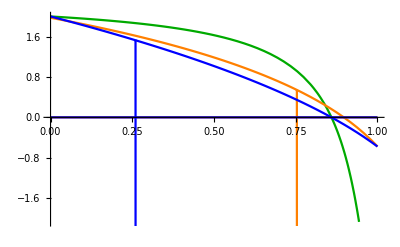

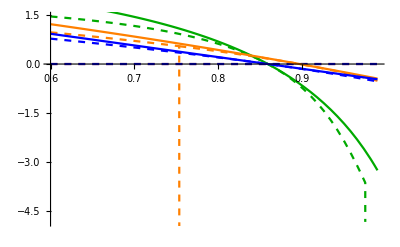

```mathematica
params={T0->6 10^6,c->10,k->5,δ->0.58,p->13};
Nsolβ=solβ/.params/.myR0->7
params1={T0->6 10^6,c->10,k->5,δ->0.58/(1-e),p->13.2};
params3={T0->6 10^6,c->10,k->5,δ->0.58,p->13.2(1-e)};
Nsolβ=solβ/.params/.myR0->7;
Nsolβ2={β->7.568978374347502*^-7(1-e)};

analR0/.params/.Nsolβ
Show[
Plot[λ[[2]]/.params1/.Nsolβ,{e,0,1},PlotStyle->Darker[Green]], (* increasing cell death in green *)
Plot[{λ/.params/.Nsolβ2},{e,0,1},PlotStyle->Orange],(* reducing infectivity in orange *)
Plot[λ/.params3/.Nsolβ,{e,0,1},PlotStyle->Blue] (* reducing viral production in blue *)
]
emin=0.6;emax=0.99;
Show[
Plot[λ[[2]]/.params1/.Nsolβ,{e,emin,emax},PlotStyle->{Darker[Green],Dashed}], (* increasing cell death in green *)
Plot[{λ/.params/.Nsolβ2},{e,emin,emax},PlotStyle->{Orange,Dashed}],(* reducing infectivity in orange *)
Plot[λ/.params3/.Nsolβ,{e,emin,emax},PlotStyle->{Blue,Dashed}], (* reducing viral production in blue *)

Plot[smallroot/.params1/.Nsolβ,{e,emin,emax},PlotStyle->Darker[Green]], (* increasing cell death in green *)
Plot[{smallroot/.params/.Nsolβ2},{e,emin,emax},PlotStyle->Orange],(* reducing infectivity in orange *)
Plot[smallroot/.params3/.Nsolβ,{e,emin,emax},PlotStyle->Blue] (* reducing viral production in blue *)
]
```